-Graphics-

```mathematica
grade[real_,guess_]:=Sort[Map[Sign,real-guess]]
```

```mathematica
r[n_]:=Table[RandomInteger[{1,9}],{n}]
```

```mathematica
arrow[1,{x_,y_}]:={Hue[0,.5],Polygon[{{x+.3,y+.1},{x+.7,y+.1},{x+.7,y+.5},{x+.9,y+.5},{x+.5,y+.9},{x+.1,y+.5},{x+.3,y+.5}}]}
```

```mathematica
arrow[-1,{x_,y_}]:={Hue[.35,.5],Polygon[{{x+.3,y+.9},{x+.7,y+.9},{x+.7,y+.5},{x+.9,y+.5},{x+.5,y+.1},{x+.1,y+.5},{x+.3,y+.5}}]}
```

```mathematica
p[t_]:={Cos[2Pi t/5],Sin[2Pi t/5]}
```

```mathematica
arrow[0,{x_,y_}]:={Hue[.6,.5],Polygon[Flatten[Transpose[{Table[{x+.5,y+.5}+.18p[i-1/4],{i,1,5}],Table[{x+.5,y+.5}+.45p[i+1/4],{i,1,5}]},{2,1,3}],1]]}
```

```mathematica
Graphics[{arrow[1,1,1],arrow[-1,2,1],arrow[0,3,1]}]
```

-Graphics-

```mathematica
pic[R_,G_]:=Style[Graphics[{
MapIndexed[Text[Style[#1,FontSize->24],#2+{5.5,.4}]&,Transpose[R],{2}],
MapIndexed[arrow[#1,#2]&,Transpose[G],{2}]
},ImageSize->250],Antialiasing->False]
```

```mathematica
For[n=1,n<10^6,n++,
r1=r[5];
r2=r[5];
r3=r[5];
r4=r[5];
r5=r[5];
answer=r[5];If[Count[answer,1]≤1&&Count[answer,9]≤1,
g1=grade[answer,r1];
g2=grade[answer,r2];
g3=grade[answer,r3];
g4=grade[answer,r4];
g5=grade[answer,r5];
If[Length[Select[Flatten[{g1,g2,g3,g4,g5}],#==0&]]<5&&Max[Count[g1,0],Count[g2,0],Count[g3,0],Count[g4,0],Count[g5,0]]≤1&&Length[Union[g1]]>1&&Length[Union[g2]]>1&&Length[Union[g3]]>1&&Length[Union[g4]]>1&&Length[Union[g5]]>1,
sol=Select[Flatten[Outer[List,Range[1,9],Range[1,9],Range[1,9],Range[1,9],Range[1,9]],4],grade[#,r1]==g1&&grade[#,r2]==g2&&grade[#,r3]==g3&&grade[#,r4]==g4&&grade[#,r5]==g5&];
If[Length[sol]==1,Print[pic[{r1,r2,r3,r4,r5},{g1,g2,g3,g4,g5}]];Print[answer];Print[]]]]]
```

## 3x3

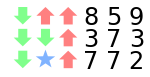

{9,6,2}

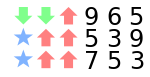

{8,5,9}

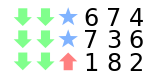

{6,3,1}

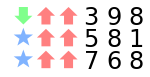

{7,8,9}

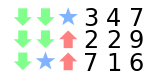

{1,4,6}

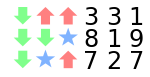

{7,1,8}

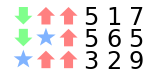

{4,6,9}

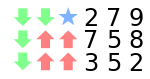

{1,6,9}

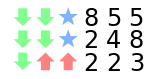

{1,4,5}

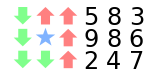

{1,9,6}

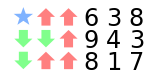

{7,3,9}

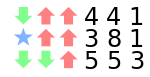

{3,9,2}

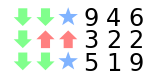

{4,1,6}

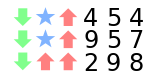

{3,5,9}

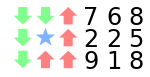

{1,2,9}

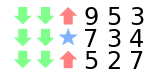

{6,1,4}

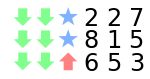

{2,1,4}

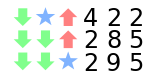

{1,9,2}

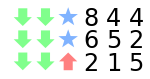

{1,4,2}

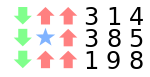

{2,8,9}

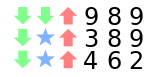

{3,9,2}

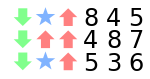

{5,9,5}

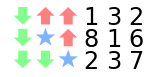

{2,2,6}

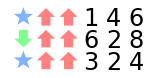

{3,4,9}

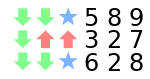

{5,1,8}

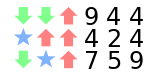

{8,2,9}

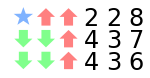

{3,2,9}

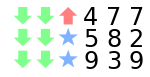

{5,3,1}

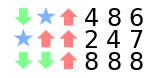

{4,4,9}

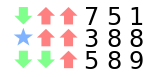

{4,9,8}

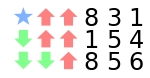

{9,3,5}

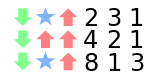

{1,3,3}

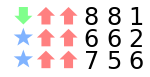

{9,6,6}

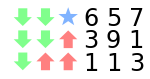

{2,5,2}

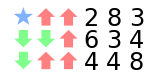

{5,9,3}

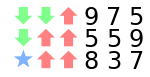

{8,6,8}

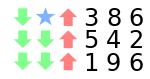

{4,8,1}

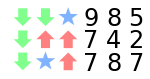

{8,8,1}

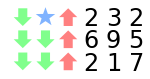

{1,3,6}

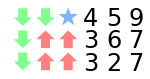

{4,1,8}

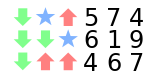

{5,1,8}

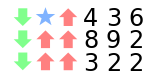

{9,1,6}

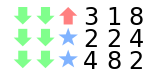

{1,2,2}

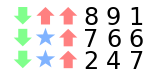

{9,4,6}

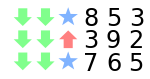

{7,5,1}

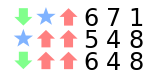

{5,7,9}

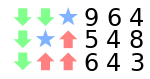

{5,5,4}

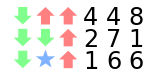

{1,5,9}

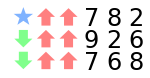

{8,8,7}

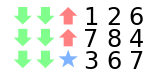

{3,1,5}

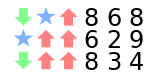

{7,6,9}

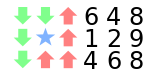

{5,1,9}

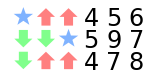

{5,8,6}

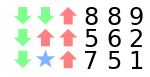

{6,9,1}

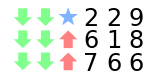

{1,2,7}

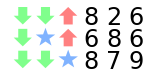

{6,1,9}

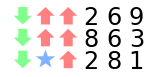

{9,7,1}

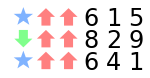

{9,4,5}

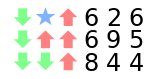

{7,1,6}

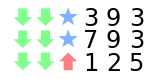

{2,1,3}

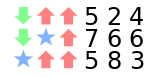

{7,9,3}

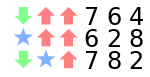

{6,8,9}

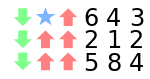

{6,9,1}

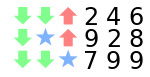

{1,2,9}

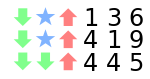

{1,2,9}

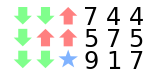

{6,1,6}

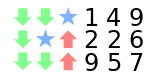

{1,2,8}

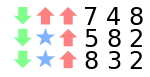

{8,8,1}

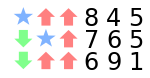

{9,5,5}

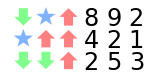

{9,2,2}

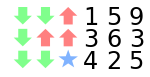

{4,1,4}

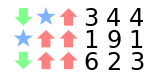

{2,9,4}

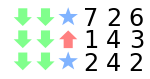

{2,2,1}

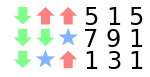

{6,2,1}

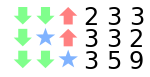

{1,5,2}

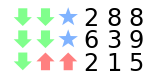

{1,3,8}

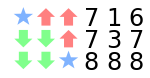

{8,2,6}

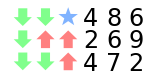

{3,8,1}

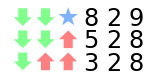

{4,1,9}

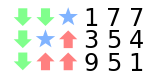

{1,6,4}

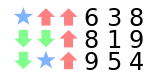

{7,5,8}

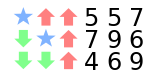

{7,5,8}

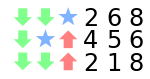

{1,6,6}

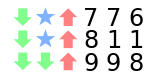

{7,1,9}

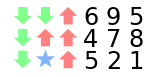

{5,1,9}

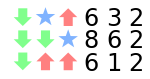

{8,3,1}

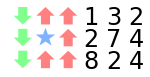

{9,7,1}

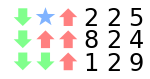

{9,1,5}

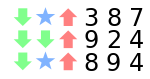

{8,1,7}

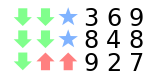

{3,3,8}

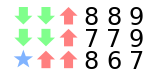

{9,6,8}

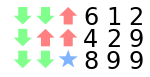

{5,9,1}

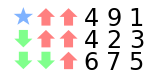

{5,9,2}

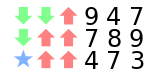

{8,9,3}

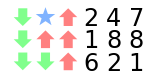

{2,1,9}

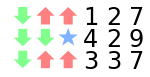

{4,1,8}

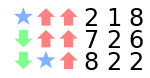

{8,1,9}

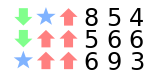

{7,9,4}

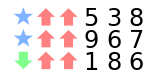

{9,7,8}

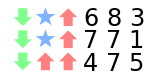

{6,9,1}

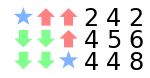

{3,4,7}

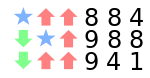

{8,9,8}

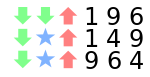

{9,4,5}

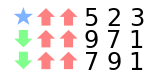

{8,8,3}

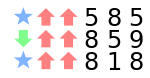

{9,8,8}

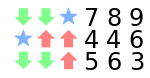

{4,5,9}

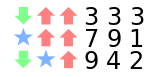

{8,9,2}

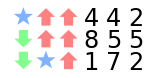

{9,6,2}

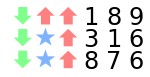

{2,9,6}

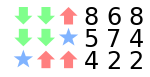

{4,7,3}

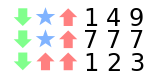

{7,1,9}

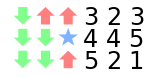

{4,1,4}

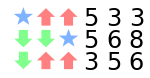

{5,4,7}

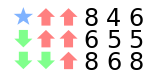

{9,4,7}

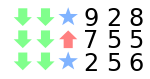

{1,2,6}

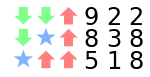

{8,1,9}

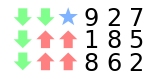

{9,1,6}

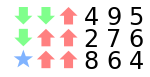

{9,8,4}

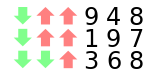

{2,5,9}

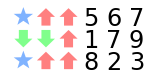

{8,6,8}

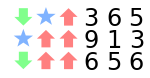

{9,6,4}

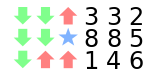

{2,8,1}

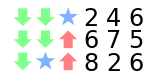

{1,3,6}

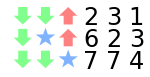

{1,2,4}

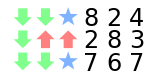

{7,1,4}

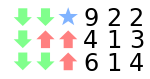

{5,2,1}

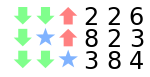

{1,8,3}

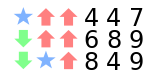

{8,9,7}

-Graphics-

{8,3,2}

-Graphics-

{8,4,9}

-Graphics-

{1,4,5}

-Graphics-

{3,9,2}

-Graphics-

{5,9,7}

-Graphics-

{2,8,4}

-Graphics-

{5,2,9}

-Graphics-

{1,6,9}

-Graphics-

{6,9,2}

-Graphics-

{9,3,3}

-Graphics-

{3,4,1}

-Graphics-

{9,3,5}

-Graphics-

{9,7,2}

-Graphics-

{5,6,1}

-Graphics-

{1,8,9}

-Graphics-

{5,3,1}

-Graphics-

{6,1,3}

-Graphics-

{9,7,2}

-Graphics-

{1,8,5}

-Graphics-

{1,5,5}

-Graphics-

{9,3,8}

-Graphics-

{4,3,6}

-Graphics-

{5,6,1}

-Graphics-

{5,5,8}

-Graphics-

{3,6,7}

-Graphics-

{5,1,9}

-Graphics-

{1,2,4}

-Graphics-

{4,5,9}

-Graphics-

{9,5,1}

-Graphics-

{7,7,9}

-Graphics-

{1,7,2}

-Graphics-

{7,9,1}

-Graphics-

{5,5,1}

-Graphics-

{1,3,5}

-Graphics-

{2,5,1}

-Graphics-

{8,3,2}

-Graphics-

{1,4,3}

-Graphics-

{6,7,8}

-Graphics-

{6,5,5}

-Graphics-

{9,4,2}

-Graphics-

{7,6,1}

-Graphics-

{7,7,9}

-Graphics-

{4,2,1}

-Graphics-

{8,9,7}

-Graphics-

{4,1,3}

-Graphics-

{2,8,1}

-Graphics-

{5,1,9}

-Graphics-

{7,9,3}

-Graphics-

{2,9,3}

-Graphics-

{1,5,9}

-Graphics-

{4,7,1}

-Graphics-

{9,8,6}

-Graphics-

{9,2,4}

-Graphics-

{9,3,5}

-Graphics-

{7,4,7}

-Graphics-

{1,6,6}

-Graphics-

{9,7,2}

-Graphics-

{2,1,4}

-Graphics-

{8,1,5}

-Graphics-

{1,4,9}

-Graphics-

{9,2,6}

-Graphics-

{7,1,9}

-Graphics-

{5,1,2}

-Graphics-

{2,6,1}

-Graphics-

{1,8,6}

-Graphics-

{4,9,1}

-Graphics-

{6,9,2}

-Graphics-

{2,4,8}

-Graphics-

{1,9,5}

-Graphics-

{1,7,2}

-Graphics-

{4,9,1}

-Graphics-

{8,8,3}

-Graphics-

{5,1,9}

-Graphics-

{8,1,6}

-Graphics-

{9,8,2}

-Graphics-

{7,5,8}

-Graphics-

{5,7,9}

-Graphics-

{2,6,1}

-Graphics-

{2,1,6}

-Graphics-

{4,9,7}

-Graphics-

{4,1,6}

-Graphics-

{3,9,1}

-Graphics-

{4,7,8}

-Graphics-

{7,3,1}

-Graphics-

{2,9,1}

-Graphics-

{8,1,9}

-Graphics-

{8,9,4}

-Graphics-

{1,6,8}

-Graphics-

{5,9,8}

-Graphics-

{5,1,3}

-Graphics-

{7,5,5}

-Graphics-

{4,1,8}

-Graphics-

{6,9,3}

-Graphics-

{2,2,1}

-Graphics-

{5,9,2}

-Graphics-

{1,4,9}

-Graphics-

{9,8,3}

-Graphics-

{1,2,8}

-Graphics-

{2,6,9}

-Graphics-

{1,4,9}

-Graphics-

{1,3,5}

-Graphics-

{9,2,4}

-Graphics-

{4,9,2}

-Graphics-

{2,1,2}

-Graphics-

{1,2,3}

-Graphics-

{2,4,2}

-Graphics-

{1,9,4}

-Graphics-

{9,4,2}

-Graphics-

{2,4,5}

-Graphics-

{3,9,1}

-Graphics-

{5,6,7}

-Graphics-

{6,1,9}

-Graphics-

{1,9,8}

-Graphics-

{1,9,5}

-Graphics-

{7,9,8}

-Graphics-

{9,1,4}

-Graphics-

{7,9,2}

-Graphics-

{8,9,1}

-Graphics-

{4,6,1}

-Graphics-

{1,9,2}

-Graphics-

{5,1,5}

-Graphics-

{5,9,1}

-Graphics-

{3,7,1}

-Graphics-

{4,3,9}

-Graphics-

{1,4,5}

-Graphics-

{5,1,2}

-Graphics-

{7,7,2}

-Graphics-

{8,9,8}

-Graphics-

{4,1,6}

-Graphics-

{8,9,4}

-Graphics-

{2,2,9}

-Graphics-

{2,9,1}

-Graphics-

{1,9,2}

-Graphics-

{7,6,1}

-Graphics-

{8,2,3}

-Graphics-

{6,4,1}

-Graphics-

{1,9,5}

-Graphics-

{3,2,1}

-Graphics-

{5,6,1}

-Graphics-

{2,9,1}

-Graphics-

{4,7,1}

-Graphics-

{4,1,6}

-Graphics-

{6,6,5}

-Graphics-

{9,1,4}

-Graphics-

{4,6,1}

-Graphics-

{4,1,4}

-Graphics-

{5,8,1}

-Graphics-

{9,6,1}

-Graphics-

{5,9,8}

-Graphics-

{5,2,6}

-Graphics-

{1,7,2}

-Graphics-

{5,1,9}

-Graphics-

{6,9,2}

-Graphics-

{8,7,9}

-Graphics-

{1,4,6}

-Graphics-

{3,1,2}

-Graphics-

{8,9,3}

-Graphics-

{8,8,6}

-Graphics-

{5,3,9}

-Graphics-

{6,5,8}

-Graphics-

{7,1,5}

-Graphics-

{1,4,5}

-Graphics-

{5,1,8}

-Graphics-

{8,9,2}

-Graphics-

{9,8,8}

-Graphics-

{6,3,9}

-Graphics-

{8,9,3}

-Graphics-

{9,3,1}

-Graphics-

{2,5,2}

-Graphics-

{7,9,8}

-Graphics-

{4,6,1}

-Graphics-

{6,9,7}

-Graphics-

{9,8,4}

-Graphics-

{9,3,1}

-Graphics-

{9,3,4}

-Graphics-

{8,2,7}

-Graphics-

{9,1,3}

-Graphics-

{9,5,1}

-Graphics-

{7,7,8}

-Graphics-

{4,8,5}

-Graphics-

{7,3,9}

-Graphics-

{7,9,8}

-Graphics-

{3,9,8}

-Graphics-

{5,4,1}

-Graphics-

{7,4,8}

-Graphics-

{6,1,8}

-Graphics-

{5,9,4}

-Graphics-

{9,2,6}

-Graphics-

{3,8,1}

-Graphics-

{6,8,1}

-Graphics-

{2,9,3}

-Graphics-

{1,2,2}

-Graphics-

{5,8,9}

-Graphics-

{5,1,4}

-Graphics-

{4,4,9}

-Graphics-

{2,1,9}

-Graphics-

{9,7,6}

-Graphics-

{7,1,9}

-Graphics-

{9,2,4}

-Graphics-

{4,9,1}

-Graphics-

{9,5,4}

-Graphics-

{3,7,9}

-Graphics-

{9,1,7}

-Graphics-

{7,3,9}

-Graphics-

{1,5,9}

-Graphics-

{1,9,8}

-Graphics-

{9,6,1}

-Graphics-

{7,2,9}

-Graphics-

{7,3,9}

-Graphics-

{5,4,3}

-Graphics-

{2,1,3}

-Graphics-

{1,7,4}

-Graphics-

{3,6,1}

-Graphics-

{1,9,8}

-Graphics-

{1,6,5}

-Graphics-

{2,4,1}

-Graphics-

{1,8,2}

-Graphics-

{8,8,9}

-Graphics-

{1,6,5}

-Graphics-

{3,3,1}

-Graphics-

{1,5,7}

-Graphics-

{3,2,1}

-Graphics-

{3,1,9}

-Graphics-

{1,5,6}

-Graphics-

{5,8,9}

-Graphics-

{6,2,1}

-Graphics-

{9,4,6}

-Graphics-

{6,1,2}

-Graphics-

{6,8,9}

-Graphics-

{4,7,9}

-Graphics-

{2,6,3}

-Graphics-

{6,1,8}

-Graphics-

{5,1,6}

-Graphics-

{7,1,9}

-Graphics-

{7,9,5}

-Graphics-

{7,1,7}

-Graphics-

{8,3,2}

-Graphics-

{1,4,4}

-Graphics-

{1,7,9}

-Graphics-

{7,8,9}

-Graphics-

{7,6,5}

-Graphics-

{8,1,4}

-Graphics-

{9,5,7}

-Graphics-

{8,1,4}

-Graphics-

{1,8,9}

-Graphics-

{5,1,8}

-Graphics-

{9,7,7}

-Graphics-

{1,9,4}

-Graphics-

{2,1,9}

-Graphics-

{5,1,6}

-Graphics-

{2,9,8}

-Graphics-

{8,1,8}

-Graphics-

{8,7,9}

-Graphics-

{5,8,2}

-Graphics-

{6,6,9}

-Graphics-

{1,9,3}

-Graphics-

{1,9,8}

-Graphics-

{6,6,1}

-Graphics-

{7,7,6}

-Graphics-

{4,7,1}

-Graphics-

{9,2,2}

-Graphics-

{7,1,8}

-Graphics-

{8,1,9}

-Graphics-

{3,2,9}

-Graphics-

{6,9,7}

-Graphics-

{1,4,4}

-Graphics-

{9,3,1}

-Graphics-

{1,4,2}

-Graphics-

{4,9,4}

-Graphics-

{2,7,1}

-Graphics-

{6,3,1}

-Graphics-

{4,3,9}

-Graphics-

{2,2,9}

-Graphics-

{8,9,4}

-Graphics-

{3,5,1}

-Graphics-

{2,3,4}

-Graphics-

{8,7,3}

-Graphics-

{5,2,1}

-Graphics-

{4,9,8}

-Graphics-

{2,1,5}

-Graphics-

{5,2,1}

-Graphics-

{9,1,2}

-Graphics-

{3,9,1}

-Graphics-

{6,1,5}

-Graphics-

{1,6,9}

-Graphics-

{3,3,9}

-Graphics-

{5,1,8}

-Graphics-

{5,8,9}

-Graphics-

{7,9,1}

-Graphics-

{4,8,1}

-Graphics-

{1,3,2}

-Graphics-

{8,1,9}

-Graphics-

{9,3,2}

-Graphics-

{5,1,4}

-Graphics-

{5,1,9}

-Graphics-

{1,7,8}

-Graphics-

{7,5,4}

-Graphics-

{9,5,3}

-Graphics-

{9,5,6}

-Graphics-

{5,9,4}

-Graphics-

{2,8,9}

-Graphics-

{7,9,5}

-Graphics-

{4,5,1}

-Graphics-

{8,5,2}

-Graphics-

{5,3,1}

-Graphics-

{8,1,7}

-Graphics-

{1,4,6}

-Graphics-

{1,7,3}

-Graphics-

{1,8,9}

-Graphics-

{1,4,2}

-Graphics-

{9,6,1}

-Graphics-

{3,9,3}

-Graphics-

{8,1,9}

-Graphics-

{1,7,9}

-Graphics-

{8,9,1}

-Graphics-

{9,8,5}

-Graphics-

{3,4,9}

-Graphics-

{2,9,8}

-Graphics-

{1,9,6}

-Graphics-

{5,5,1}

-Graphics-

{3,2,1}

-Graphics-

{4,6,1}

-Graphics-

{9,7,1}

-Graphics-

{2,9,4}

-Graphics-

{9,8,1}

-Graphics-

{5,3,8}

-Graphics-

{1,9,3}

-Graphics-

{3,3,9}

-Graphics-

{2,6,9}

-Graphics-

{1,2,6}

-Graphics-

{5,8,1}

-Graphics-

{7,8,3}

-Graphics-

{2,6,5}

-Graphics-

{1,3,7}

-Graphics-

{9,5,5}

-Graphics-

{8,9,8}

-Graphics-

{2,3,8}

-Graphics-

{6,1,4}

-Graphics-

{8,9,4}

-Graphics-

{2,8,1}

-Graphics-

{7,1,3}

-Graphics-

{9,3,2}

-Graphics-

{4,9,1}

-Graphics-

{5,1,4}

-Graphics-

{4,4,9}

-Graphics-

{9,2,2}

-Graphics-

{1,7,3}

-Graphics-

{1,6,8}

-Graphics-

{1,5,8}

-Graphics-

{1,5,9}

-Graphics-

{1,8,7}

-Graphics-

{1,5,2}

-Graphics-

{3,7,6}

-Graphics-

{9,7,1}

-Graphics-

{7,1,6}

-Graphics-

{5,6,9}

-Graphics-

{9,4,2}

-Graphics-

{7,9,3}

-Graphics-

{1,8,8}

-Graphics-

{1,6,4}

-Graphics-

{9,4,8}

-Graphics-

{7,9,3}

-Graphics-

{1,2,6}

-Graphics-

{9,7,6}

-Graphics-

{9,2,1}

-Graphics-

{3,3,9}

-Graphics-

{8,9,4}

-Graphics-

{9,8,8}

-Graphics-

{9,1,6}

-Graphics-

{9,7,3}

-Graphics-

{1,9,4}

-Graphics-

{4,9,1}

-Graphics-

{6,4,9}

-Graphics-

{6,8,5}

-Graphics-

{1,5,3}

-Graphics-

{7,1,7}

-Graphics-

{6,1,4}

-Graphics-

{2,8,1}

-Graphics-

{1,4,2}

-Graphics-

{4,5,9}

-Graphics-

{6,8,9}

-Graphics-

{1,8,3}

-Graphics-

{7,1,2}

-Graphics-

{9,8,2}

-Graphics-

{6,9,4}

-Graphics-

{4,2,1}

-Graphics-

{5,7,1}

-Graphics-

{9,1,3}

-Graphics-

{1,9,7}

-Graphics-

{5,1,3}

-Graphics-

{6,1,5}

-Graphics-

{1,5,5}

-Graphics-

{1,7,5}

-Graphics-

{3,4,1}

-Graphics-

{8,1,7}

-Graphics-

{6,6,9}

-Graphics-

{9,4,1}

-Graphics-

{2,4,5}

-Graphics-

{5,8,1}

-Graphics-

{1,7,2}

-Graphics-

{4,9,4}

-Graphics-

{1,7,9}

-Graphics-

{4,1,7}

-Graphics-

{6,6,8}

-Graphics-

{1,6,4}

-Graphics-

{3,1,9}

-Graphics-

{4,9,4}

-Graphics-

{6,9,1}

-Graphics-

{4,4,1}

-Graphics-

{8,5,8}

-Graphics-

{1,9,5}

-Graphics-

{5,9,6}

-Graphics-

{3,6,9}

-Graphics-

{3,2,6}

-Graphics-

{9,5,1}

-Graphics-

{9,5,3}

-Graphics-

{7,9,7}

-Graphics-

{1,9,2}

-Graphics-

{1,4,9}

-Graphics-

{1,4,7}

-Graphics-

{2,1,9}

-Graphics-

{9,4,1}

-Graphics-

{1,6,3}

-Graphics-

{4,1,4}

-Graphics-

{2,6,9}

-Graphics-

{8,9,4}

-Graphics-

{1,9,3}

-Graphics-

{1,7,6}

-Graphics-

{9,3,3}

-Graphics-

{5,9,2}

-Graphics-

{8,7,5}

-Graphics-

{4,6,8}

-Graphics-

{2,3,1}

-Graphics-

{1,9,4}

-Graphics-

{1,2,2}

-Graphics-

{7,6,1}

-Graphics-

{6,3,3}

-Graphics-

{8,1,9}

-Graphics-

{8,1,3}

-Graphics-

{6,7,9}

-Graphics-

{1,6,4}

-Graphics-

{1,6,7}

-Graphics-

{1,6,7}

-Graphics-

{3,9,8}

-Graphics-

{3,9,1}

-Graphics-

{9,1,8}

-Graphics-

{9,5,3}

-Graphics-

{9,6,4}

-Graphics-

{9,1,6}

-Graphics-

{1,8,7}

-Graphics-

{9,3,4}

-Graphics-

{1,4,9}

-Graphics-

{8,1,7}

-Graphics-

{3,1,9}

-Graphics-

{9,8,1}

-Graphics-

{1,8,9}

-Graphics-

{2,1,9}

-Graphics-

{4,9,6}

-Graphics-

{9,6,1}

-Graphics-

{4,2,1}

-Graphics-

{6,7,1}

-Graphics-

{6,1,2}

-Graphics-

{9,7,2}

-Graphics-

{1,4,3}

-Graphics-

{4,1,6}

-Graphics-

{9,2,7}

-Graphics-

{1,9,6}

-Graphics-

{2,1,3}

-Graphics-

{9,1,6}

-Graphics-

{5,1,4}

-Graphics-

{7,1,9}

-Graphics-

{9,5,3}

-Graphics-

{1,2,5}

-Graphics-

{8,3,1}

-Graphics-

{8,1,5}

-Graphics-

{8,7,1}

-Graphics-

{1,8,2}

-Graphics-

{2,6,1}

-Graphics-

{9,7,1}

-Graphics-

{5,1,9}

-Graphics-

{9,7,7}

-Graphics-

{2,2,4}

-Graphics-

{4,9,2}

-Graphics-

{9,2,5}

-Graphics-

{1,6,4}

-Graphics-

{1,4,2}

-Graphics-

{5,3,9}

-Graphics-

{7,5,9}

-Graphics-

{3,3,1}

-Graphics-

{8,9,6}

-Graphics-

{3,1,9}

-Graphics-

{5,1,8}

-Graphics-

{9,3,6}

-Graphics-

{1,4,6}

-Graphics-

{9,5,8}

-Graphics-

{9,7,1}

-Graphics-

{6,9,1}

-Graphics-

{5,8,1}

-Graphics-

{3,3,1}

-Graphics-

{6,9,8}

-Graphics-

{4,4,9}

-Graphics-

{7,9,3}

-Graphics-

{9,1,5}

-Graphics-

{9,3,7}

-Graphics-

{4,5,1}

-Graphics-

{6,6,1}

-Graphics-

{9,4,2}

-Graphics-

{6,9,4}

-Graphics-

{5,9,4}

-Graphics-

{3,3,1}

-Graphics-

{8,5,9}

-Graphics-

{7,9,5}

-Graphics-

{8,1,8}

-Graphics-

{2,9,5}

-Graphics-

{6,5,9}

-Graphics-

{1,6,9}

-Graphics-

{9,1,6}

-Graphics-

{2,3,4}

-Graphics-

{6,1,3}

-Graphics-

{1,9,2}

-Graphics-

{6,9,2}

-Graphics-

{1,9,2}

-Graphics-

{3,6,2}

-Graphics-

{5,7,4}

-Graphics-

{7,9,8}

-Graphics-

{8,4,9}

-Graphics-

{6,9,2}

-Graphics-

{7,6,9}

-Graphics-

{8,9,4}

-Graphics-

{7,9,7}

-Graphics-

{8,1,9}

-Graphics-

{4,8,3}

-Graphics-

{5,9,3}

-Graphics-

{4,3,1}

-Graphics-

{9,6,7}

-Graphics-

{9,4,1}

-Graphics-

{7,2,9}

-Graphics-

{3,3,1}

-Graphics-

{5,8,9}

-Graphics-

{6,1,8}

-Graphics-

{1,2,5}

-Graphics-

{2,5,8}

-Graphics-

{2,4,1}

-Graphics-

{9,1,4}

-Graphics-

{9,2,8}

-Graphics-

{8,1,9}

-Graphics-

{1,7,4}

-Graphics-

{3,9,6}

-Graphics-

{1,3,9}

-Graphics-

{9,2,1}

-Graphics-

{8,1,7}

-Graphics-

{2,4,1}

-Graphics-

{3,9,8}

-Graphics-

{2,9,1}

-Graphics-

{6,4,9}

-Graphics-

{7,5,5}

-Graphics-

{8,1,9}

-Graphics-

{3,1,8}

-Graphics-

{1,7,4}

-Graphics-

{4,2,9}

-Graphics-

{7,9,8}

-Graphics-

{3,8,1}

-Graphics-

{5,3,1}

-Graphics-

{5,9,5}

-Graphics-

{3,3,1}

-Graphics-

{3,7,2}

-Graphics-

{1,3,8}

-Graphics-

{1,2,2}

-Graphics-

{9,8,6}

-Graphics-

{9,4,7}

-Graphics-

{6,7,2}

-Graphics-

{4,1,3}

-Graphics-

{1,9,2}

-Graphics-

{1,6,6}

-Graphics-

{1,9,7}

-Graphics-

{3,9,3}

-Graphics-

{9,3,5}

-Graphics-

{1,9,3}

-Graphics-

{6,1,5}

-Graphics-

{9,5,4}

-Graphics-

{6,6,6}

-Graphics-

{9,8,7}

-Graphics-

{2,8,1}

-Graphics-

{9,8,1}

-Graphics-

{1,2,2}

-Graphics-

{4,1,3}

-Graphics-

{1,6,3}

-Graphics-

{4,6,1}

-Graphics-

{9,7,6}

-Graphics-

{9,5,2}

-Graphics-

{4,9,3}

-Graphics-

{8,6,6}

-Graphics-

{1,7,9}

-Graphics-

{2,1,8}

-Graphics-

{7,6,2}

-Graphics-

{6,1,6}

-Graphics-

{5,5,3}

-Graphics-

{8,6,1}

-Graphics-

{1,9,8}

-Graphics-

{2,6,9}

-Graphics-

{7,7,9}

-Graphics-

{4,9,6}

-Graphics-

{5,4,1}

-Graphics-

{2,8,1}

-Graphics-

{4,5,1}

-Graphics-

{2,9,1}

-Graphics-

{4,5,1}

-Graphics-

{4,9,5}

-Graphics-

{4,9,1}

-Graphics-

{9,4,5}

-Graphics-

{2,9,8}

-Graphics-

{2,2,1}

-Graphics-

{6,7,1}

-Graphics-

{2,1,5}

-Graphics-

{3,4,3}

-Graphics-

{6,3,1}

-Graphics-

{2,8,9}

-Graphics-

{9,7,1}

-Graphics-

{4,7,3}

-Graphics-

{1,3,4}

-Graphics-

{8,1,7}

-Graphics-

{1,8,6}

-Graphics-

{7,7,2}

-Graphics-

{2,5,8}

-Graphics-

{9,7,2}

-Graphics-

{2,4,9}

-Graphics-

{9,3,3}

-Graphics-

{9,3,1}

-Graphics-

{9,6,8}

-Graphics-

{7,9,6}

-Graphics-

{9,2,8}

-Graphics-

{3,1,9}

-Graphics-

{1,8,6}

-Graphics-

{1,3,8}

-Graphics-

{5,8,8}

-Graphics-

{3,6,1}

-Graphics-

{8,5,1}

-Graphics-

{1,3,5}

-Graphics-

{9,3,1}

-Graphics-

{5,5,9}

-Graphics-

{6,3,9}

-Graphics-

{3,1,9}

-Graphics-

{9,8,8}

-Graphics-

{4,4,9}

-Graphics-

{9,1,8}

-Graphics-

{8,9,3}

-Graphics-

{4,9,1}

-Graphics-

{9,7,4}

-Graphics-

{9,6,4}

-Graphics-

{5,9,5}

-Graphics-

{1,9,5}

-Graphics-

{2,3,9}

-Graphics-

{7,5,3}

-Graphics-

{4,4,9}

-Graphics-

{8,5,1}

-Graphics-

{9,3,2}

-Graphics-

{9,5,4}

-Graphics-

{2,2,1}

-Graphics-

{1,8,5}

-Graphics-

{9,5,1}

-Graphics-

{4,1,8}

-Graphics-

{3,9,8}

-Graphics-

{5,4,9}

-Graphics-

{3,1,7}

-Graphics-

{6,1,4}

-Graphics-

{4,8,1}

-Graphics-

{5,1,9}

-Graphics-

{8,3,8}

-Graphics-

{9,4,6}

-Graphics-

{3,7,9}

-Graphics-

{3,7,6}

-Graphics-

{8,1,4}

-Graphics-

{6,6,9}

-Graphics-

{4,9,1}

-Graphics-

{1,4,8}

-Graphics-

{3,4,1}

-Graphics-

{8,9,4}

-Graphics-

{9,5,1}

-Graphics-

{6,9,1}

-Graphics-

{3,2,8}

-Graphics-

{8,4,1}

-Graphics-

{7,9,1}

-Graphics-

{7,1,6}

-Graphics-

{1,9,8}

-Graphics-

{4,2,5}

-Graphics-

{8,4,2}

-Graphics-

{5,9,1}

-Graphics-

{1,9,7}

-Graphics-

{5,7,8}

-Graphics-

{3,1,7}

-Graphics-

{1,5,8}

-Graphics-

{9,4,4}

-Graphics-

{9,2,6}

-Graphics-

{9,6,8}

-Graphics-

{8,9,8}

-Graphics-

{9,7,7}

-Graphics-

{1,9,8}

-Graphics-

{9,5,3}

-Graphics-

{7,3,9}

-Graphics-

{6,4,9}

-Graphics-

{3,1,8}

-Graphics-

{5,8,9}

-Graphics-

{7,1,5}

-Graphics-

{1,8,4}

-Graphics-

{8,9,2}

-Graphics-

{7,3,1}

-Graphics-

{1,2,2}

-Graphics-

{3,1,6}

-Graphics-

{2,1,7}

-Graphics-

{8,6,9}

-Graphics-

{3,8,9}

-Graphics-

{8,1,3}

-Graphics-

{8,1,6}

-Graphics-

{3,1,3}

-Graphics-

{6,9,4}

-Graphics-

{1,2,3}

-Graphics-

{4,1,9}

-Graphics-

{7,7,9}

-Graphics-

{1,6,8}

-Graphics-

{1,6,4}

-Graphics-

{2,9,1}

-Graphics-

{9,7,6}

-Graphics-

{8,6,4}

-Graphics-

{3,9,6}

-Graphics-

{5,2,1}

-Graphics-

{9,1,4}

-Graphics-

{5,5,9}

-Graphics-

{8,1,8}

-Graphics-

{1,9,2}

-Graphics-

{9,7,8}

-Graphics-

{1,4,9}

-Graphics-

{1,9,3}

-Graphics-

{6,8,2}

-Graphics-

{6,5,1}

-Graphics-

{5,1,9}

-Graphics-

{5,9,5}

-Graphics-

{8,1,2}

-Graphics-

{5,3,8}

-Graphics-

{3,1,4}

-Graphics-

{8,7,3}

-Graphics-

{2,1,8}

-Graphics-

{6,1,8}

-Graphics-

{8,6,5}

-Graphics-

{6,8,1}

-Graphics-

{9,7,5}

-Graphics-

{6,2,3}

-Graphics-

{6,7,1}

-Graphics-

{3,1,8}

-Graphics-

{9,8,1}

-Graphics-

{7,9,7}

-Graphics-

{1,9,7}

-Graphics-

{1,5,2}

-Graphics-

{1,6,3}

-Graphics-

{9,2,8}

-Graphics-

{1,9,2}

-Graphics-

{1,5,3}

-Graphics-

{2,2,9}

-Graphics-

{9,5,8}

-Graphics-

{1,3,3}

-Graphics-

{3,6,9}

-Graphics-

{1,3,3}

-Graphics-

{4,5,9}

-Graphics-

{6,3,1}

-Graphics-

{7,4,3}

-Graphics-

{1,5,9}

-Graphics-

{9,1,5}

-Graphics-

{3,1,4}

-Graphics-

{4,9,5}

-Graphics-

{9,4,7}

-Graphics-

{3,2,7}

-Graphics-

{9,3,7}

-Graphics-

{1,9,7}

-Graphics-

{1,5,2}

-Graphics-

{2,8,9}

-Graphics-

{7,3,7}

-Graphics-

{2,9,1}

-Graphics-

{4,1,9}

-Graphics-

{3,9,3}

-Graphics-

{7,3,5}

-Graphics-

{9,6,3}

-Graphics-

{9,6,2}

-Graphics-

{8,9,4}

-Graphics-

{2,9,8}

-Graphics-

{4,2,9}

-Graphics-

{9,1,7}

-Graphics-

{9,8,1}

-Graphics-

{7,7,1}

-Graphics-

{9,3,8}

-Graphics-

{1,5,4}

-Graphics-

{8,7,4}

-Graphics-

{8,1,3}

-Graphics-

{4,9,1}

-Graphics-

{8,9,2}

-Graphics-

{4,2,9}

-Graphics-

{9,4,2}

-Graphics-

{4,1,9}

-Graphics-

{9,2,1}

-Graphics-

{6,4,7}

-Graphics-

{5,1,3}

-Graphics-

{7,7,1}

-Graphics-

{7,1,6}

-Graphics-

{6,4,1}

-Graphics-

{1,3,4}

-Graphics-

{4,9,6}

-Graphics-

{9,1,4}

-Graphics-

{4,2,1}

-Graphics-

{5,3,3}

-Graphics-

{1,3,9}

-Graphics-

{9,6,1}

-Graphics-

{6,9,8}

-Graphics-

{1,6,8}

-Graphics-

{1,6,3}

-Graphics-

{3,4,1}

-Graphics-

{3,3,9}

-Graphics-

{9,2,8}

-Graphics-

{1,8,8}

-Graphics-

{1,7,7}

-Graphics-

{2,7,1}

-Graphics-

{7,5,8}

-Graphics-

{5,4,3}

-Graphics-

{3,4,9}

-Graphics-

{6,9,1}

-Graphics-

{2,1,5}

-Graphics-

{2,3,9}

-Graphics-

{9,8,8}

-Graphics-

{1,3,4}

-Graphics-

{8,1,8}

-Graphics-

{8,8,9}

-Graphics-

{6,3,1}

-Graphics-

{1,8,3}

-Graphics-

{1,3,7}

-Graphics-

{2,8,7}

-Graphics-

{1,8,2}

-Graphics-

{3,1,2}

-Graphics-

{8,1,2}

-Graphics-

{3,1,6}

-Graphics-

{4,3,9}

-Graphics-

{3,3,9}

-Graphics-

{4,9,2}

-Graphics-

{6,1,2}

-Graphics-

{4,1,4}

-Graphics-

{7,4,9}

-Graphics-

{1,4,6}

-Graphics-

{8,2,9}

-Graphics-

{2,1,5}

-Graphics-

{1,4,5}

-Graphics-

{1,5,4}

-Graphics-

{9,6,4}

-Graphics-

{9,4,4}

-Graphics-

{5,1,2}

-Graphics-

{7,3,9}

-Graphics-

{6,2,9}

-Graphics-

{2,9,1}

-Graphics-

{7,5,1}

-Graphics-

{5,4,9}

-Graphics-

{5,5,2}

-Graphics-

{2,1,9}

-Graphics-

{9,7,5}

-Graphics-

{5,1,6}

-Graphics-

{7,1,4}

-Graphics-

{2,1,5}

-Graphics-

{6,9,8}

-Graphics-

{9,4,7}

-Graphics-

{2,1,9}

-Graphics-

{7,6,1}

-Graphics-

{3,2,6}

-Graphics-

{5,9,2}

-Graphics-

{5,7,1}

-Graphics-

{5,1,7}

-Graphics-

{9,8,6}

-Graphics-

{6,9,1}

-Graphics-

{9,7,2}

-Graphics-

{5,1,3}

-Graphics-

{4,9,6}

-Graphics-

{4,1,2}

-Graphics-

{6,3,9}

-Graphics-

{9,3,8}

-Graphics-

{7,7,9}

-Graphics-

{3,4,8}

-Graphics-

{7,5,1}

-Graphics-

{3,1,7}

-Graphics-

{5,2,1}

-Graphics-

{8,5,1}

-Graphics-

{8,8,5}

-Graphics-

{6,7,2}

-Graphics-

{3,9,8}

-Graphics-

{9,3,4}

-Graphics-

{8,9,1}

-Graphics-

{2,6,1}

-Graphics-

{2,1,5}

-Graphics-

{8,1,3}

-Graphics-

{1,7,8}

-Graphics-

{9,3,6}

-Graphics-

{2,9,7}

-Graphics-

{6,3,1}

-Graphics-

{5,1,8}

-Graphics-

{8,6,1}

-Graphics-

{6,1,4}

-Graphics-

{6,1,7}

-Graphics-

{7,9,1}

-Graphics-

{1,9,7}

-Graphics-

{1,5,4}

-Graphics-

{1,9,7}

-Graphics-

{5,9,1}

-Graphics-

{8,2,9}

-Graphics-

{4,9,1}

-Graphics-

{1,3,3}

-Graphics-

{4,9,2}

-Graphics-

{9,5,6}

-Graphics-

{9,8,1}

-Graphics-

{7,6,9}

-Graphics-

{5,3,1}

-Graphics-

{5,4,1}

-Graphics-

{3,7,3}

-Graphics-

{7,4,1}

-Graphics-

{3,9,3}

-Graphics-

{4,1,8}

-Graphics-

{1,9,3}

-Graphics-

{6,5,1}

-Graphics-

{3,1,5}

-Graphics-

{7,7,9}

-Graphics-

{9,5,1}

-Graphics-

{4,9,6}

-Graphics-

{4,9,1}

-Graphics-

{2,9,5}

-Graphics-

{6,4,9}

-Graphics-

{1,5,9}

-Graphics-

{1,8,9}

-Graphics-

{1,4,6}

-Graphics-

{6,7,9}

-Graphics-

{8,1,8}

-Graphics-

{9,6,1}

-Graphics-

{5,9,8}

-Graphics-

{9,1,5}

-Graphics-

{7,1,8}

-Graphics-

{9,3,1}

-Graphics-

{2,9,3}

-Graphics-

{6,6,4}

-Graphics-

{3,8,9}

-Graphics-

{3,5,1}

-Graphics-

{9,1,2}

-Graphics-

{6,1,7}

-Graphics-

{6,7,1}

-Graphics-

{4,1,6}

-Graphics-

{9,6,5}

-Graphics-

{7,2,9}

-Graphics-

{9,8,3}

-Graphics-

{1,8,3}

-Graphics-

{8,6,6}

-Graphics-

{8,9,1}

-Graphics-

{5,1,3}

-Graphics-

{3,1,9}

-Graphics-

{5,6,1}

-Graphics-

{4,2,1}

-Graphics-

{3,5,1}

-Graphics-

{6,2,1}

-Graphics-

{2,5,1}

-Graphics-

{2,3,7}

-Graphics-

{1,6,9}

-Graphics-

{7,9,1}

-Graphics-

{9,8,1}

-Graphics-

{5,2,9}

-Graphics-

{6,1,6}

-Graphics-

{3,1,9}

-Graphics-

{6,9,1}

-Graphics-

{9,7,1}

-Graphics-

{5,3,3}

-Graphics-

{2,2,3}

-Graphics-

{5,9,1}

-Graphics-

{4,9,1}

-Graphics-

{2,9,8}

-Graphics-

{5,7,1}

-Graphics-

{1,3,2}

-Graphics-

{9,6,1}

-Graphics-

{5,8,9}

-Graphics-

{1,3,6}

-Graphics-

{9,6,1}

-Graphics-

{5,7,2}

-Graphics-

{4,3,9}

-Graphics-

{2,3,1}

-Graphics-

{4,8,9}

-Graphics-

{9,6,8}

-Graphics-

{9,4,6}

-Graphics-

{3,1,4}

-Graphics-

{6,7,9}

-Graphics-

{4,1,2}

-Graphics-

{3,6,9}

-Graphics-

{3,5,8}

-Graphics-

{2,8,9}

-Graphics-

{9,4,8}

-Graphics-

{7,6,9}

-Graphics-

{2,1,4}

-Graphics-

{2,1,6}

-Graphics-

{6,1,5}

-Graphics-

{3,8,1}

-Graphics-

{4,6,1}

-Graphics-

{5,7,6}

-Graphics-

{3,9,1}

-Graphics-

{6,8,1}

-Graphics-

{5,1,2}

-Graphics-

{5,8,9}

-Graphics-

{1,5,7}

-Graphics-

{4,9,8}

-Graphics-

{9,1,4}

-Graphics-

{2,9,7}

-Graphics-

{9,1,8}

-Graphics-

{2,1,5}

-Graphics-

{7,3,1}

-Graphics-

{2,3,9}

-Graphics-

{8,7,1}

-Graphics-

{2,9,4}

-Graphics-

{9,1,6}

-Graphics-

{3,3,9}

-Graphics-

{8,1,9}

-Graphics-

{7,5,5}

-Graphics-

{4,1,5}

-Graphics-

{9,8,5}

-Graphics-

{9,1,4}

-Graphics-

{1,6,9}

-Graphics-

{7,1,5}

-Graphics-

{6,7,1}

-Graphics-

{8,3,7}

-Graphics-

{5,9,1}

-Graphics-

{3,9,1}

-Graphics-

{2,9,7}

-Graphics-

{2,4,9}

-Graphics-

{8,1,7}

-Graphics-

{9,8,1}

-Graphics-

{5,8,1}

-Graphics-

{1,7,7}

-Graphics-

{6,6,2}

-Graphics-

{3,8,1}

-Graphics-

{3,1,9}

-Graphics-

{2,9,3}

-Graphics-

{7,6,8}

-Graphics-

{6,4,6}

-Graphics-

{4,9,5}

-Graphics-

{4,9,4}

-Graphics-

{8,9,7}

-Graphics-

{5,9,2}

-Graphics-

{4,1,2}

-Graphics-

{3,9,7}

-Graphics-

{5,6,4}

-Graphics-

{3,1,9}

-Graphics-

{3,9,2}

-Graphics-

{9,3,1}

-Graphics-

{9,4,8}

-Graphics-

{4,6,1}

-Graphics-

{4,2,9}

-Graphics-

{1,7,2}

-Graphics-

{8,9,8}

-Graphics-

{9,1,7}

-Graphics-

{1,8,4}

-Graphics-

{8,9,7}

-Graphics-

{1,9,8}

-Graphics-

{6,2,1}

-Graphics-

{4,1,9}

-Graphics-

{9,7,6}

-Graphics-

{4,1,3}

-Graphics-

{7,4,6}

-Graphics-

{1,7,9}

-Graphics-

{6,1,6}

-Graphics-

{9,5,6}

-Graphics-

{8,9,7}

-Graphics-

{7,2,2}

-Graphics-

{5,7,1}

-Graphics-

{7,9,8}

-Graphics-

{6,9,4}

-Graphics-

{4,8,7}

-Graphics-

{9,1,5}

-Graphics-

{1,4,9}

-Graphics-

{6,9,1}

-Graphics-

{5,1,8}

-Graphics-

{6,4,1}

-Graphics-

{9,3,4}

-Graphics-

{9,7,4}

-Graphics-

{5,4,1}

-Graphics-

{9,5,5}

-Graphics-

{1,7,4}

-Graphics-

{8,5,9}

-Graphics-

{1,7,5}

-Graphics-

{6,9,7}

-Graphics-

{3,5,9}

-Graphics-

{7,9,6}

-Graphics-

{3,1,2}

-Graphics-

{1,5,9}

-Graphics-

{7,3,6}

-Graphics-

{9,8,1}

-Graphics-

{9,2,6}

-Graphics-

{7,1,2}

-Graphics-

{1,3,3}

-Graphics-

{1,6,8}

-Graphics-

{8,9,3}

-Graphics-

{5,1,4}

-Graphics-

{9,5,6}

-Graphics-

{9,6,1}

-Graphics-

{4,1,9}

-Graphics-

{4,2,9}

-Graphics-

{9,2,2}

-Graphics-

{9,1,4}

-Graphics-

{1,5,8}

-Graphics-

{2,4,9}

-Graphics-

{7,7,4}

-Graphics-

{4,9,3}

-Graphics-

{6,9,1}

-Graphics-

{8,9,8}

-Graphics-

{1,5,7}

-Graphics-

{6,5,9}

-Graphics-

{2,8,4}

-Graphics-

{4,6,3}

-Graphics-

{2,3,9}

-Graphics-

{7,9,1}

-Graphics-

{9,4,1}

-Graphics-

{1,6,6}

-Graphics-

{4,1,4}

-Graphics-

{9,1,8}

-Graphics-

{8,9,5}

-Graphics-

{6,1,5}

-Graphics-

{8,5,4}

-Graphics-

{3,1,7}

-Graphics-

{5,9,5}

-Graphics-

{6,7,7}

-Graphics-

{9,2,1}

-Graphics-

{8,8,1}

-Graphics-

{4,9,1}

-Graphics-

{8,6,2}

-Graphics-

{7,7,9}

-Graphics-

{3,9,1}

-Graphics-

{2,2,4}

-Graphics-

{6,9,3}

-Graphics-

{1,2,9}

-Graphics-

{3,4,5}

-Graphics-

{9,4,5}

-Graphics-

{7,1,5}

-Graphics-

{4,5,2}

-Graphics-

{8,4,2}

-Graphics-

{9,7,4}

-Graphics-

{5,7,8}

-Graphics-

{7,3,6}

-Graphics-

{7,5,7}

-Graphics-

{9,5,3}

-Graphics-

{3,1,5}

-Graphics-

{6,5,1}

-Graphics-

{1,9,4}

-Graphics-

{6,1,5}

-Graphics-

{3,2,7}

-Graphics-

{1,2,2}

-Graphics-

{7,3,1}

-Graphics-

{1,6,2}

-Graphics-

{4,7,9}

-Graphics-

{5,2,9}

-Graphics-

{1,3,3}

-Graphics-

{2,8,9}

-Graphics-

{8,9,7}

-Graphics-

{4,2,2}

-Graphics-

{8,4,8}

-Graphics-

{6,8,9}

-Graphics-

{8,8,6}

-Graphics-

{9,8,5}

-Graphics-

{7,5,1}

-Graphics-

{4,3,1}

-Graphics-

{1,4,3}

-Graphics-

{9,8,5}

-Graphics-

{7,9,6}

-Graphics-

{1,6,8}

-Graphics-

{5,6,7}

-Graphics-

{7,7,2}

-Graphics-

{1,9,7}

-Graphics-

{2,1,2}

-Graphics-

{5,1,5}

-Graphics-

{3,2,9}

-Graphics-

{9,1,5}

-Graphics-

{6,1,9}

-Graphics-

{7,7,1}

-Graphics-

{6,9,6}

-Graphics-

{1,5,4}

-Graphics-

{1,8,3}

-Graphics-

{9,5,4}

-Graphics-

{2,1,8}

-Graphics-

{9,2,5}

-Graphics-

{4,9,5}

-Graphics-

{4,5,4}

-Graphics-

{1,9,3}

-Graphics-

{9,7,4}

-Graphics-

{1,5,9}

-Graphics-

{6,6,1}

-Graphics-

{4,9,6}

-Graphics-

{2,9,8}

-Graphics-

{7,9,2}

-Graphics-

{7,5,1}

-Graphics-

{9,6,3}

-Graphics-

{4,3,1}

-Graphics-

{9,1,8}

-Graphics-

{7,1,3}

-Graphics-

{3,5,7}

-Graphics-

{8,3,5}

-Graphics-

{1,4,7}

-Graphics-

{7,4,8}

-Graphics-

{7,9,1}

-Graphics-

{5,4,9}

-Graphics-

{4,1,6}

-Graphics-

{5,4,9}

-Graphics-

{1,4,6}

-Graphics-

{7,3,1}

-Graphics-

{3,4,1}

-Graphics-

{5,7,1}

-Graphics-

{7,6,4}

-Graphics-

{7,1,5}

-Graphics-

{9,5,1}

-Graphics-

{5,7,9}

-Graphics-

{8,1,3}

-Graphics-

{8,1,3}

-Graphics-

{4,1,9}

-Graphics-

{3,6,9}

-Graphics-

{6,3,4}

-Graphics-

{6,4,9}

-Graphics-

{3,5,9}

-Graphics-

{6,1,7}

-Graphics-

{2,2,1}

-Graphics-

{6,1,8}

-Graphics-

{3,1,8}

-Graphics-

{9,6,1}

-Graphics-

{4,1,7}

-Graphics-

{1,8,6}

-Graphics-

{8,1,4}

-Graphics-

{1,3,9}

-Graphics-

{2,9,1}

-Graphics-

{1,5,9}

-Graphics-

{9,6,7}

-Graphics-

{5,2,9}

-Graphics-

{4,9,5}

-Graphics-

{9,4,5}

-Graphics-

{1,6,9}

-Graphics-

{5,5,7}

-Graphics-

{2,9,8}

-Graphics-

{5,9,4}

-Graphics-

{9,5,8}

-Graphics-

{4,1,3}

-Graphics-

{9,7,1}

-Graphics-

{8,9,3}

-Graphics-

{2,8,9}

-Graphics-

{9,3,3}

-Graphics-

{4,9,3}

-Graphics-

{8,3,1}

$Aborted

## 4x4

-Graphics-

{1,5,5,4}

-Graphics-

{3,3,9,6}

-Graphics-

{6,6,5,9}

-Graphics-

{7,3,1,2}

-Graphics-

{2,3,6,2}

-Graphics-

{1,4,2,6}

-Graphics-

{1,3,2,2}

-Graphics-

{4,5,3,9}

-Graphics-

{3,3,5,6}

-Graphics-

{9,6,8,2}

-Graphics-

{8,9,7,3}

-Graphics-

{7,2,6,5}

-Graphics-

{7,8,9,8}

-Graphics-

{8,1,5,9}

-Graphics-

{4,7,5,4}

-Graphics-

{2,7,8,1}

-Graphics-

{8,1,2,8}

-Graphics-

{9,2,6,4}

-Graphics-

{1,9,7,2}

-Graphics-

{1,6,7,5}

-Graphics-

{4,8,9,6}

-Graphics-

{9,7,6,7}

-Graphics-

{3,1,7,8}

-Graphics-

{3,3,1,6}

-Graphics-

{5,2,2,2}

-Graphics-

{4,6,5,7}

-Graphics-

{5,5,8,9}

-Graphics-

{7,5,9,5}

-Graphics-

{8,6,4,1}

-Graphics-

{7,3,9,2}

-Graphics-

{1,9,7,3}

## 5x5

-Graphics-

{8,4,8,7,5}

-Graphics-

{4,1,5,5,9}

-Graphics-

{6,4,7,4,9}

-Graphics-

{7,7,1,8,9}

-Graphics-

{6,9,7,3,5}

-Graphics-

{7,5,1,9,6}

-Graphics-

{3,8,8,9,1}

-Graphics-

{9,1,8,3,2}

-Graphics-

{1,9,5,5,6}

-Graphics-

{8,7,3,2,8}

-Graphics-

{7,9,4,7,7}